#### Get data from TrivPathToISO (with Tmat = TmatBrownTypo)

```mathematica
PrintFigures=True;
```

```mathematica
mdir
odir=FileNameJoin[{mdir,"pdf_print"}]
otag=FileNameJoin[{odir,"DirectPath_supp_2"}]
```

```mathematica
SigCurve=TET;
```

```mathematica
Sig1==TET
Sig2==CUBE
Tmat1==Closest[Tmat,Sig1]
Tmat2==Closest[Tmat,Sig2]
```

```mathematica
dt
```

#### Check the beta for the peak of the discretized curve

```mathematica
betamax =Max[βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree&/@Ranget]
```

#### Slope of each segment

```mathematica
MatrixNote[Tmat]
Ranget
dt
TableForm[Join[{{"   t","  βTET"}},{PaddedForm[#,{2,2}],PaddedForm[Round[βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree,.001],{4,3}]}&/@Ranget]]
```

```mathematica
MatrixNote[Tmat]
Ranget
dt
plot=Graphics[{PointSize[.015],
Line[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget],
{ColorData["Rainbow"][0/6],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
Point[{#,0}]&/@Ranget},Axes->True,AxesOrigin->{t1,0},AspectRatio->.5,ImageSize->500,Ticks->{Range[0,1,.2],Range[0,8,2]},TicksStyle->14]
```

```mathematica
(*npts =10000;
AlphaMONOvalues=Sort[Table[Alpha[Tmat2,{RandomReal[{-π,π}],RandomReal[{0,π}]},MONO]/Degree,{k,npts}]];
Take[AlphaMONOvalues,5]
Take[AlphaMONOvalues,-5]*)
```

```mathematica
cmin=0;cmax=21; dc=3;
contoursx=Range[cmin,cmax,dc];
MaxForScalingx=cmax-dc;
eye=20xyztp[{30,65}];
```

```mathematica
AngRad=.05;
ShiftToEye=.02;
tkns=.01; (* tkns only affects XISO *)
```

#### balls on bottom

```mathematica
MatrixNote[Tmat]
contoursx
MaxForScalingx
PrintEye;
```

```mathematica
tIs0=Show[{cpMONO[Tmat1,contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[Sig1,UT[Tmat,Sig1],ShiftToEye,eye]]},options]
```

```mathematica
tIsPt2onBottom=Show[cpMONO[TT[.2,Tmat1,Tmat2],contoursx,MaxForScalingx, plotpoints, contourstyle],options]
```

```mathematica
tIsPt4onBottom=Show[cpMONO[TT[.4,Tmat1,Tmat2],contoursx,MaxForScalingx, plotpoints, contourstyle],options]
```

```mathematica
tIsPt6onBottom=Show[cpMONO[TT[.6,Tmat1,Tmat2],contoursx,MaxForScalingx, plotpoints, contourstyle],options]
```

```mathematica
tIsPt8onBottom=Show[cpMONO[TT[.8,Tmat1,Tmat2],contoursx,MaxForScalingx, plotpoints, contourstyle],options]
```

```mathematica
tIs1=Show[{cpMONO[Tmat2,contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[Sig2,UT[Tmat,Sig2],ShiftToEye,eye]]},options]
```

#### balls on top

```mathematica
tIsPt2onTop=Show[{cpMONO[Closest[TT[.2,Tmat1,Tmat2],SigCurve],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve,UT[TT[.2,Tmat1,Tmat2],SigCurve],ShiftToEye,eye]]},options]
```

```mathematica
tIsPt4onTop=Show[{cpMONO[Closest[TT[.4,Tmat1,Tmat2],SigCurve],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve,UT[TT[.4,Tmat1,Tmat2],SigCurve],ShiftToEye,eye]]},options]
```

```mathematica
Ranget[[13]]
tIsPt6onTop=Show[{cpMONO[Closest[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve,UT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve],ShiftToEye,eye]]},options]
```

```mathematica
tIsPt8onTop=Show[{cpMONO[Closest[TT[.8,Tmat1,Tmat2],SigCurve],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve,UT[TT[.8,Tmat1,Tmat2], SigCurve],ShiftToEye,eye]]},options]
```

```mathematica
MatrixNote[Tmat]
Ranget
contoursx
MaxForScalingx
PrintEye;
dy=1;  (* line segment *)
dyb=dy+0.;  (* ball *)
px=Graphics[{PointSize[.013],
 {PointSize[.001],Point/@{{.1,-3 betamax},{.9,4.5 betamax}}},  (* fake points - see also AspectRatio *)
(* Line[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget], *)
{HueOfΣ[SigCurve],Line[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]},
{HueOfΣ[SigCurve],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
Point[{#,0}]&/@Ranget,
Line[{{#,0},{#,-dy}}]&/@Range[0,1,.2],
Line[{{Ranget[[#]],           βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree},
    {Ranget[[#]],dy+βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree}}]&/@{1,5,9,13,17,21},
Line[{{0,0},{1,0}}],
Text[Style["(0, 0)",18],{-.05,0}],
Text[Style["(1, 0)",18],{1.05,0}],
Inset[tIsPt2onTop,{.2,dyb+βT[TT[.2,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt4onTop,{.4,dyb+βT[TT[.4,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt6onTop,{.6,dyb+βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt8onTop,{.8,dyb+βT[TT[.8,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIs0,{0,dyb},Center,.18],,
Inset[tIs1,{1,dyb},Center,.18],
Inset[tIsPt2onBottom,{.2,-dyb},Center,.18],
Inset[tIsPt4onBottom,{.4,-dyb},Center,.18],
Inset[tIsPt6onBottom,{.6,-dyb},Center,.18],
Inset[tIsPt8onBottom,{.8,-dyb},Center,.18],
Inset[tIs0,{0,-dyb},Center,.18],
Inset[tIs1,{1,-dyb},Center,.18],
(* TRIV base curve *)
{HueOfΣ[TRIV],Line[{{0,0},{1,0}}]},
{HueOfΣ[TRIV],Point[{#,0}]&/@Ranget}
},Axes->False,AspectRatio->0.5,ImageSize->1000,PlotRange->All] ;
If[PrintFigures,Export[otag<>".pdf",px],px]
```

## Brown: dt = 0.05, Tmat1=TTET, Tmat2=TCUBE, ListSigma={MONO,TET} [supp2]

#### From BC_Superlattice.nb (dt = 0.2)

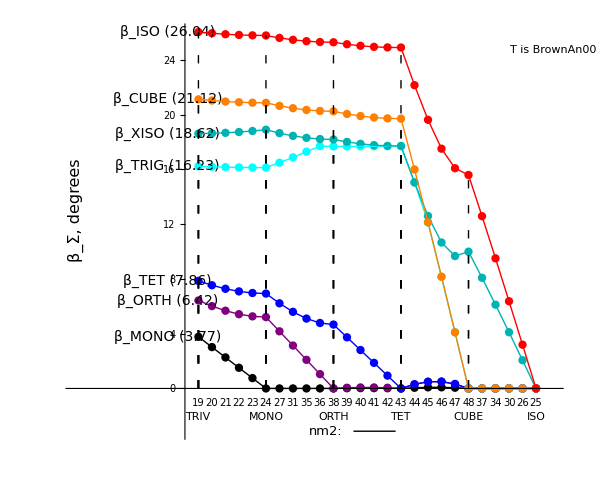

#### From BC_DirectPath.nb